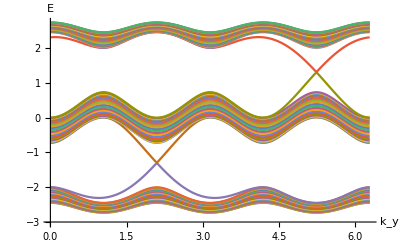

```mathematica
(* p=1, q=5, open boundary*)
Na=60;
V0=2;
pq=1./3;
Ham=Table[0,{i,1,Na},{j,1,Na}];
Do[Ham[[i,i]]=V0 Cos[2Pi pq i+ky],{i,1,Na}]
Do[Ham[[i+1,i]]=-1;Ham[[i,i+1]]=-1.;,{i,1,Na-1}]
MatrixForm[Ham];
num=201;
del=N[2Pi/(num-1)];
kya=Table[(i-1) del,{i,1,num}];
En=Table[Eigenvalues[Ham/.ky-> kya[[i]]],{i,1,num}];
da=Table[{kya[[i]],Sort[Re[En[[i]]]][[j]]},{j,1,Na},{i,1,num}];
ListLinePlot[da,AxesOrigin-> {0,-3},AxesLabel-> {"k_y","E"}]
```

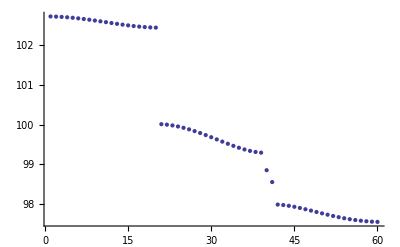

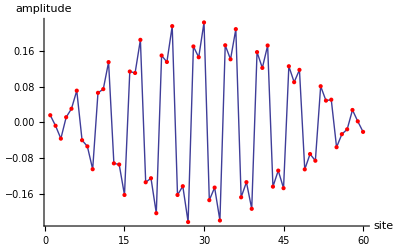

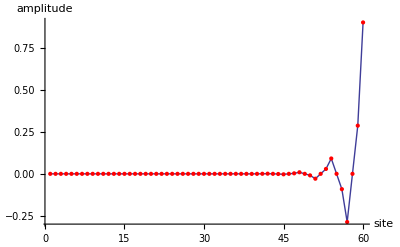

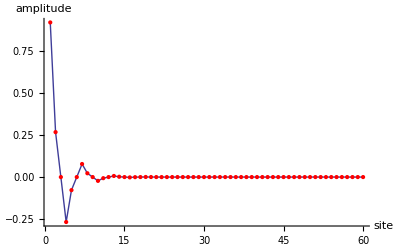

```mathematica
lg=100.IdentityMatrix[Na];
ev1=Eigensystem[(Ham+lg)/.{ky-> 2}];
ListPlot[ev1[[1]]](*all eigenvalues*)
ListLinePlot[ev1[[2,39]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,40]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,41]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
```

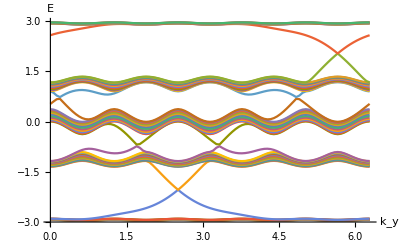

```mathematica
(* p=1, q=3, open boundary*)
Na=60;
V0=2;
pq=1./5;
Ham=Table[0,{i,1,Na},{j,1,Na}];
Do[Ham[[i,i]]=V0 Cos[2Pi pq i+ky],{i,1,Na}]
Do[Ham[[i+1,i]]=-1;Ham[[i,i+1]]=-1.;,{i,1,Na-1}]
MatrixForm[Ham];
num=101;
del=N[2Pi/(num-1)];
kya=Table[(i-1) del,{i,1,num}];
En=Table[Eigenvalues[Ham/.ky-> kya[[i]]],{i,1,num}];
da=Table[{kya[[i]],Sort[Re[En[[i]]]][[j]]},{j,1,Na},{i,1,num}];
ListLinePlot[da,AxesOrigin-> {0,-3},AxesLabel-> {"k_y","E"}]
```

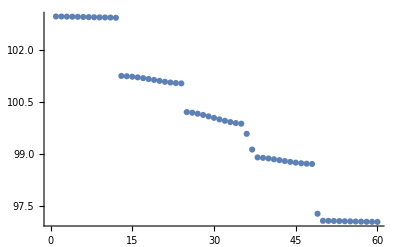

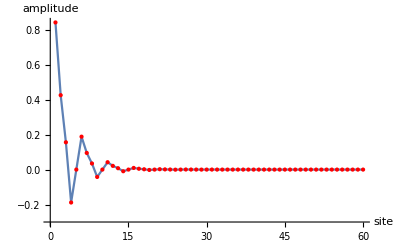

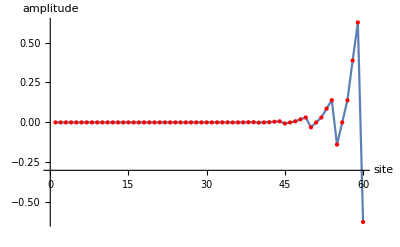

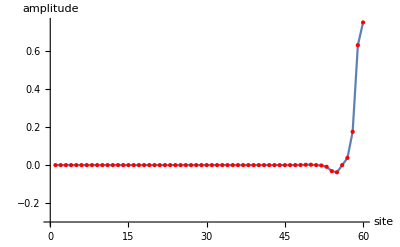

```mathematica
lg=100.IdentityMatrix[Na];
ev1=Eigensystem[(Ham+lg)/.{ky-> 3.5}];
ListPlot[ev1[[1]]](*all eigenvalues*)
ListLinePlot[ev1[[2,36]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,37]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,49]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
```

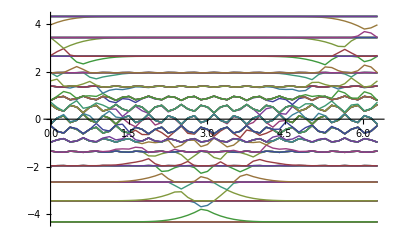

```mathematica
Na=120;
V0=2.8;
pq=1./15;
Ham=Table[0,{i,1,Na},{j,1,Na}];
Do[Ham[[i,i]]=V0 Cos[2Pi pq i+ky],{i,1,Na}]
Do[Ham[[i+1,i]]=-1;Ham[[i,i+1]]=-1.;,{i,1,Na-1}]
MatrixForm[Ham];
num=51;
del=N[2Pi/(num-1)];
kya=Table[(i-1) del,{i,1,num}];
En=Table[Eigenvalues[Ham/.ky-> kya[[i]]],{i,1,num}];
da=Table[{kya[[i]],Sort[Re[En[[i]]]][[j]]},{j,1,Na},{i,1,num}];
ListLinePlot[da]
```

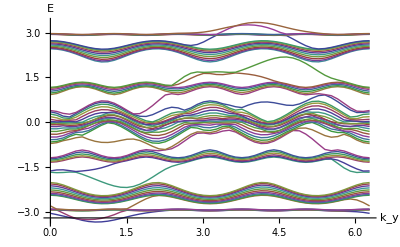

```mathematica
Na=62;
V0=2;
pq1=1./3;
pq2=1./5;
Ham=Table[0,{i,1,Na},{j,1,Na}];
Do[Ham[[i,i]]=V0 Cos[2Pi pq1 i+ky],{i,1,Na/2}]
Do[Ham[[i,i]]=V0 Cos[2Pi pq2 i+ky],{i,Na/2+1,Na}]
Do[Ham[[i+1,i]]=-1;Ham[[i,i+1]]=-1.;,{i,1,Na-1}]
Ham[[1,Na]]=-1.;
Ham[[Na,1]]=-1.;
MatrixForm[Ham];
num=51;
del=N[2Pi/(num-1)];
kya=Table[(i-1) del,{i,1,num}];
En=Table[Eigenvalues[Ham/.ky-> kya[[i]]],{i,1,num}];
da=Table[{kya[[i]],Sort[Re[En[[i]]]][[j]]},{j,1,Na},{i,1,num}];
ListLinePlot[da,AxesOrigin-> {0,-3.2},AxesLabel-> {"k_y","E"}]
```

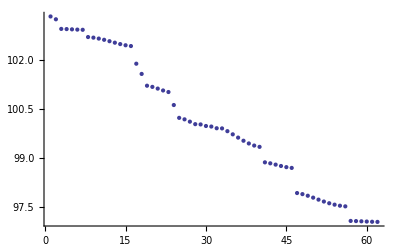

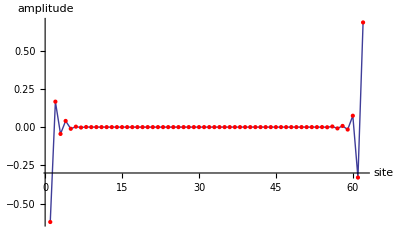

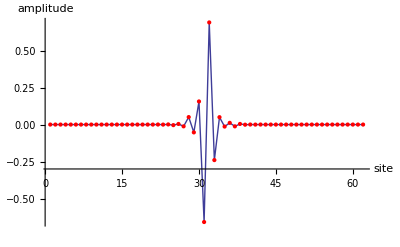

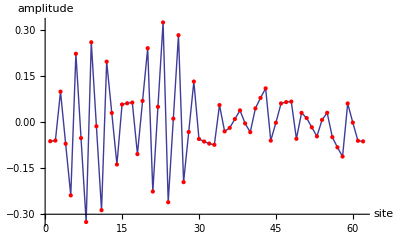

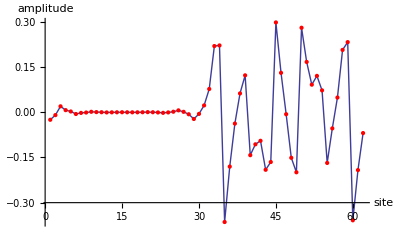

```mathematica
lg=100.IdentityMatrix[Na];
ev1=Eigensystem[(Ham+lg)/.{ky-> 4.}];
ListPlot[ev1[[1]]]
ListLinePlot[ev1[[2,1]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,2]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,30]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
ListLinePlot[ev1[[2,43]],PlotRange-> All,Mesh->All,MeshStyle->Directive[PointSize[Large],Red],AxesLabel-> {"site","amplitude"},AxesOrigin-> {0,-0.3},BaseStyle->{FontSize->16}]
```

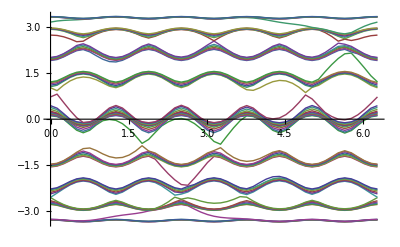

```mathematica
Na=60;
V0=2.5;
pq1=1./5;
pq2=2./5;
Ham=Table[0,{i,1,Na},{j,1,Na}];
Do[Ham[[i,i]]=V0 Cos[2Pi pq1 i+ky],{i,1,Na/2}]
Do[Ham[[i,i]]=V0 Cos[2Pi pq2 i+ky],{i,Na/2+1,Na}]
Do[Ham[[i+1,i]]=-1;Ham[[i,i+1]]=-1.;,{i,1,Na-1}]
MatrixForm[Ham];
num=51;
del=N[2Pi/(num-1)];
kya=Table[(i-1) del,{i,1,num}];
En=Table[Eigenvalues[Ham/.ky-> kya[[i]]],{i,1,num}];
da=Table[{kya[[i]],Sort[Re[En[[i]]]][[j]]},{j,1,Na},{i,1,num}];
ListLinePlot[da]
```